```mathematica
8Quantity[377, "Kilobits"]5
```

15080 kb

```mathematica
8 Quantity[377, "Kilobits"]/Quantity[1, "Seconds"] 5
```

15080 kb/s

```mathematica
UnitConvert[Out[2], "Megabytes"]
```

377/200 MB/s

```mathematica
QuantityMagnitude[Quantity[377/200, ("Megabytes")/("Seconds")]]
```

377/200

```mathematica
N[377/200]
```

1.885

```mathematica
CountryData["Chile", "ExportCommodities"]
```

{Chemicals,Copper,Fish,Fruit,Paper,Pulp,Wine}

```mathematica
CountryData["Chile", "ExportPartnersFractions"]
```

{China→0.142,United States→0.113,Japan→0.104,Brazil→0.059,South Korea→0.057,Netherlands→0.052,Italy→0.044}

```mathematica
CountryData["Chile", "ExportValue"]
```

7.03136×10^10 $

```mathematica
TimeSeries[{1, 1}]
```

TimeSeries[…]

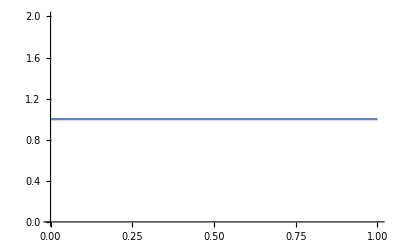

```mathematica
ListLinePlot[TimeSeries[…]]
```

```mathematica
TimeSeries[{1, 1}, {2, 3}, {3, 1}]
```

TimeSeries::nonopt: Options expected (instead of {3,1}) beyond position 2 in TimeSeries[{1,1},{2,3},{3,1}]. An option must be a rule or a list of rules.

TimeSeries[{1,1},{2,3},{3,1}]

```mathematica
TimeSeries@{{1,1},{2,3},{3,1}}
```

TimeSeries[…]

```mathematica
RegularlySampledQ[TimeSeries[…]]
```

True

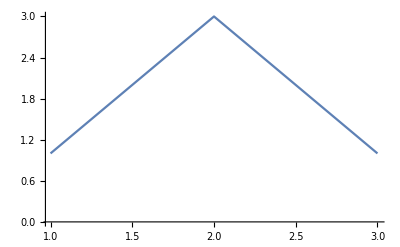

```mathematica
ListLinePlot[TimeSeries[…]]
```

```mathematica
CountryData["UnitedStates", "GDPSectorFractions"]
```

{AgriculturalValueAdded→0.0107568,ConstructionValueAdded→0.047555,IndustrialValueAdded→0.169453,MiscellaneousValueAdded→0.56096,TradeValueAdded→0.151864,TransportationValueAdded→0.0594111}

```mathematica
CountryData["UnitedStates", "GDP"]
```

1.86245×10^13 $

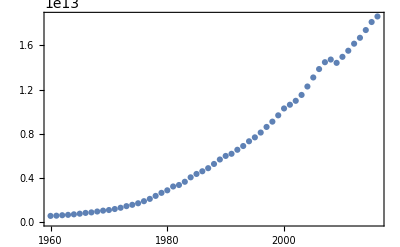

```mathematica
DateListPlot[
CountryData["UnitedStates", {"GDP", All}], Joined->False]
```

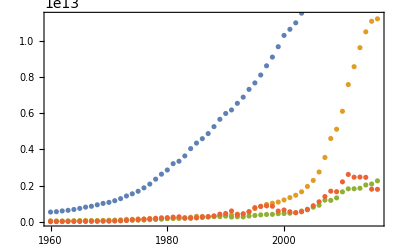

```mathematica
DateListPlot[{
CountryData["UnitedStates",{"GDP", All}],
CountryData["China",{"GDP", All}],
CountryData["India", {"GDP", All}],
CountryData["Brazil", {"GDP", All}]
}, Joined->False]
```

```mathematica
DateListPlot[{
CountryData["UnitedStates",{"GDP", All}],
CountryData["China",{"GDP", All}],
CountryData["India", {"GDP", All}],
CountryData["Brazil", {"GDP", All}]
}, Joined->False]
```

-Graphics-

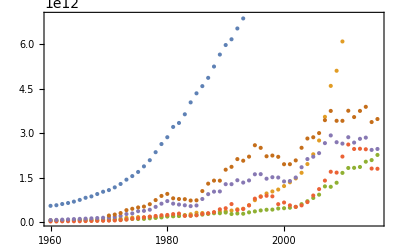

```mathematica
DateListPlot[
Table[
CountryData[c,{"GDP", All}],
{c, {"UnitedStates", "China", "India", "Brazil", "France", "Germany"}}]
, Joined->False]
```

```mathematica
us=CountryData["UnitedStates", {"GDP", All}];
```

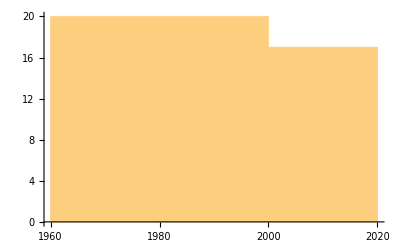

```mathematica
DateHistogram[%22]
```

```mathematica
Differences[us]
```

TimeSeries[…]

```mathematica
Differences[FinancialData["NASDAQ:GOOG", "Price", All]]
```

{{{0,0,1},1.52594},{{0,0,3},-3.01196},1275,{{0,0,1},-3.89001},{{0,0,1},1.89001}}
 |  |  |  |

```mathematica
us[[4]]
```

11.3

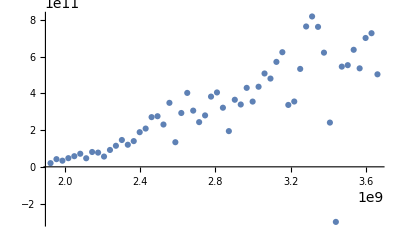

```mathematica
ListPlot[Differences@us, Joined->False]
```

```mathematica
FinancialData["^GSPC", "Price"]
```

2870.72

```mathematica
sp=Map[Last,FinancialData["^GSPC", "Price", All]]
```

{16.66,16.85,16.93,17444,2884.05,2879.42,2870.72}
 |  |  |  |

```mathematica
With[{stock="^GSPC"},
With[{list=FinancialData[stock, "Price", All]},
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list]
}]]]
```

{{{1950,1,3},0.190001},{{1950,1,4},0.0799999},17446,{{2019,5,8},-8.69995}}
 |  |  |  |

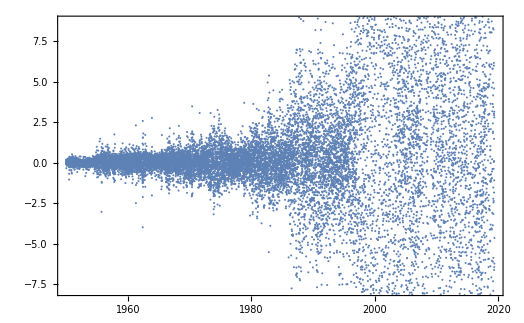

```mathematica
DateListPlot[
Out[30], Joined->False]
```

```mathematica
Table[func->func@Map[Last,Out@30],
{func, {Max, Min, Mean, Median, Variance ,StandardDeviation}}]
```

{Max→116.6,Min→-113.19,Mean→0.163566,Median→0.0499992,Variance→81.4063,StandardDeviation→9.02255}

```mathematica
Table[func->func@Map[Last,Out@30],
{func, {Max, Min, Mean, Median, Variance ,StandardDeviation, GeometricMean, HarmonicMean}}]
```

{Max→116.6,Min→-113.19,Mean→0.163566,Median→0.0499992,Variance→81.4063,StandardDeviation→9.02255,GeometricMean→0.,HarmonicMean→0}

```mathematica
With[{stock="^GSPC"},
With[{list=FinancialData[stock, "Price", All]},
Differences@
Map[Last,list]
]]
```

{0.190001,0.0799999,0.0499992,17443,-48.4199,-4.63013,-8.69995}
 |  |  |  |

```mathematica
Standardize@Out@34
```

{0.00292985,-0.0092619,-0.012587,17444,-0.531302,-0.982374}
 |  |  |  |

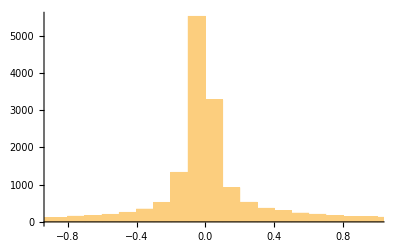

```mathematica
Histogram[%35]
```

```mathematica
Sort@Out@35
```

{-12.5634,-11.8607,-11.1746,17443,10.1331,11.523,12.905}
 |  |  |  |

```mathematica
CentralMoment[%37,2]
```

0.999943

```mathematica
Table[func->func@Map[Last,Out@30],
{func, {Max, Min, Mean, Median, Variance ,StandardDeviation}}]
```

{Max→116.6,Min→-113.19,Mean→0.163566,Median→0.0499992,Variance→81.4063,StandardDeviation→9.02255}

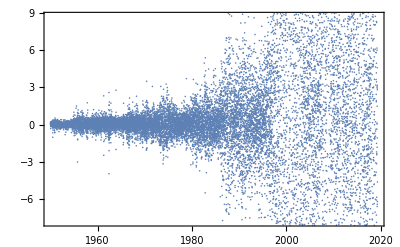

```mathematica
DateListPlot[
Tooltip@Out[30], Joined->False]
```

```mathematica
Table[func->func@Map[Last,Out@30],
{func, {Max, Min, Mean, Median, Variance ,StandardDeviation, Quantile}}]
```

Quantile::argb: Quantile[{0.190001,0.0799999,0.0499992,«45»,0.200001,0.039999,«17399»}] called with 1 arguments; between 2 and 3 arguments are expected.

{Max→116.6,5,Quantile→Quantile[{0.190001,17447,-8.69995}]}
 |  |  |  |

```mathematica
Table[func->func@Map[Last,Out@30],
{func, 
{Max, Min, Mean, Median, Variance ,StandardDeviation, Quantile[#,{1/4,2/4,3/4,90/100}]&}}]
```

{Max→116.6,Min→-113.19,Mean→0.163566,Median→0.0499992,Variance→81.4063,StandardDeviation→9.02255,(Quantile[#1,{1/4,2/4,3/4,90/100}]&)→{-0.740005,0.0499992,1.00999,6.46997}}

```mathematica
Sort@Out@30
```

{{{1950,1,3},0.190001},{{1950,1,4},0.0799999},17446,{{2019,5,8},-8.69995}}
 |  |  |  |

```mathematica
Sort@Out@30
```

```mathematica
Table[func->func@Map[Last,Out@37],
{func, 
{Max, Min, Mean, Median, Variance ,StandardDeviation, Quantile[#,{1/4,2/4,3/4,90/100}]&}}]
```

Last::normal: Nonatomic expression expected at position 1 in Last[-12.5634].

Last::normal: Nonatomic expression expected at position 1 in Last[-11.8607].

Last::normal: Nonatomic expression expected at position 1 in Last[-11.1746].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Median::rectn: Rectangular array of real numbers is expected at position 1 in Median[{Last[-12.5634],Last[-11.8607],Last[-11.1746],«46»,Last[-5.38468],«17399»}].

$Aborted

```mathematica
Sort@Out@34
```

{-113.19,-106.85,-100.66,17443,91.59,104.13,116.6}
 |  |  |  |

```mathematica
Table[func->func@Map[Last,Out@45],
{func, 
{Max, Min, Mean, Median, Variance ,StandardDeviation, Quantile[#,{1/4,2/4,3/4,90/100}]&}}]
```

Last::normal: Nonatomic expression expected at position 1 in Last[-113.19].

Last::normal: Nonatomic expression expected at position 1 in Last[-106.85].

Last::normal: Nonatomic expression expected at position 1 in Last[-100.66].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Median::rectn: Rectangular array of real numbers is expected at position 1 in Median[{Last[-113.19],Last[-106.85],Last[-100.66],«46»,Last[-48.4199],«17399»}].

$Aborted

```mathematica
Table[func->func@Out@45,
{func, 
{Max, Min, Mean, Median, Variance ,StandardDeviation, Quantile[#,{1/4,2/4,3/4,90/100}]&}}]
```

{Max→116.6,Min→-113.19,Mean→0.163566,Median→0.0499992,Variance→81.4063,StandardDeviation→9.02255,(Quantile[#1,{1/4,2/4,3/4,90/100}]&)→{-0.740005,0.0499992,1.00999,6.46997}}

```mathematica
Quantile[Out@45,{1/4,2/4,3/4,90/100,99/100}]
```

{-0.740005,0.0499992,1.00999,6.46997,29.1101}

```mathematica
Quantile[Out@45,{1/4,2/4,3/4,90/100,99/100,999/1000}]
```

{-0.740005,0.0499992,1.00999,6.46997,29.1101,51.78}

```mathematica
Sum[9^i,{i, 1, 10}]
```

3922632450

```mathematica
Sum[9*10^i,{i, 1, 10}]
```

99999999990

```mathematica
Sum[9*10^i,{i, 0, 10}]
```

99999999999

```mathematica
Sum[9*10^i,{i, 0, 6}]
```

9999999

```mathematica
Sum[(9*10^i)/10^i,{i, 0, 6}]
```

63

```mathematica
Sum[10^i,{i, 0, 6}]
```

1111111

```mathematica
∑_(i=0)^6 9 10^i
```

9999999

```mathematica
With[{a=6},
(∑_(i=0)^a 9 10^i)/10^a]
```

9999999/1000000

```mathematica
Table[
(∑_(i=0)^a 9 10^i)/10^a,{a,1,6}]
```

{99/10,999/100,9999/1000,99999/10000,999999/100000,9999999/1000000}

```mathematica
Table[
(∑_(i=0)^a 9 10^i)/10^(a+1),{a,1,6}]
```

{99/100,999/1000,9999/10000,99999/100000,999999/1000000,9999999/10000000}

```mathematica
Quantile[Out@45, 
Table[
(∑_(i=0)^a 9 10^i)/10^(a+1),{a,1,6}]]
```

{29.1101,51.78,104.13,116.6,116.6,116.6}

```mathematica
Quantile[Out@45, 
Join[Table[a/10,{a, 1, 9}],Table[
(∑_(i=0)^a 9 10^i)/10^(a+1),{a,1,4}]]]
```

{-5.20996,-1.22,-0.440002,-0.119995,0.0499992,0.239998,0.619995,1.81,6.46997,29.1101,51.78,104.13,116.6}

```mathematica
Interpolation@FinancialData["NASDAQ:GOOG", "Price", All]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

InterpolatingFunction[…]

```mathematica
Out@66[[5]]
```

Part::partd: Part specification 66⟦5⟧ is longer than depth of object.

Out::intm: Machine-sized integer expected at position 1 in Out[66⟦5⟧].

Out[66⟦5⟧]

```mathematica
Out@66[x][[5]]
```

Part::partw: Part 5 of 66[x] does not exist.

Out::intm: Machine-sized integer expected at position 1 in Out[66[x]⟦5⟧].

Out[66[x]⟦5⟧]

```mathematica
Out[66][x][[5]]
```

Part::partw: Part 5 of InterpolatingFunction[{{2014.,2019.},{1.,12.},{1.,31.}},«3»,{Automatic}][x] does not exist.

InterpolatingFunction[…][x]⟦5⟧

```mathematica
Mean[RandomSample[Out[45], 10]]
```

0.011001

```mathematica
Mean[RandomSample[Out[45], 10]]
```

-5.887